General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

NDSolve::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {u,W[u],NDSolve`s$165873[u]} = {0.0000149012,-2.64722674251935×10^119810,-1}.

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

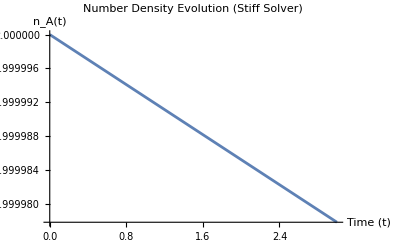

```mathematica
sigmaV=2.0 10^-26; 
MDM =100; (*Mass of particle A[GeV]*)
gX=2; (*Number of degrees of freedom*)
c=2.99792458 10^8 ;(* Speed of light in m/s *)
hbar=1.054571817 10^-34 ;(*Reduced Planck constant in J⋅s*)
k_B=1.380649 10^-23 ;(* Boltzmann constant in J/K*)
M_Pl=np.sqrt(hbar*c/(8*np.pi*G_N)); (*Reduced Planck mass in kg*)
H0=68.4*(1/3.086 10^19)*(6.58 10^-16)*(10^-9); (*in GeV*)
h=0.684;
G_eV=6.7*10^-39;
gX=2;

(*Function to find effective DOF of SM during freezeout*)
SetDirectory[NotebookDirectory[]];
data=Import["sm_dof_freezeout.csv"];
TValues=data[[All,1]];
gValues=data[[All,2]];

gStar:=Interpolation[Transpose[{TValues,gValues}]];


(*Define the rate equation for number density of particle A*)
nEQ[x_, mDM_] = gX*(mDM^3)* N[BesselK[2, x]]/(2 * π^2 * x);
sCov[x_, mDM_] = (2*π^2/45)*gStar[mDM/x]*((mDM/x)^3);
YEQ[x_,mDM_] = nEQ[x, mDM]/sCov[x,mDM];
f[x_, mDM_]:=If[x<1000,YEQ[mDM/Exp[u], mDM]^,0];

(*Define the rate equation for number density of particle X*)
rateEquation[W_,u_,sigmaV_, mDM_]:=Exp[-u]*(2.76 10^35)*sigmaV*mDM*Sqrt[gStar[mDM/Exp[u]]]*(f[mDM/Exp[u],mDM]*Exp[-W] - Exp[W]);

(*Initial conditions for number density*)
W0=Log[YEQ[1,MDM]]; (*Initial number density[particles/cm^3]*)

(*Solve the rate equation numerically using stiffness handling*)
sol=NDSolve[
{W'[u]==rateEquation[W[u], u, sigmaV, MDM],W[0]==W0},
W,
{u,0,3},  
Method->"StiffnessSwitching" (*Specify the stiffness solver*)
];
(*Extract and plot the solution*)
Wsol = W /. sol;

Plot[Log10[MDM*Exp[Wsol[[1]][u]]/Exp[W0]],{u,0,3},PlotLabel->"Number Density Evolution (Stiff Solver)",AxesLabel->{"Time (t)","n_A(t)"},PlotRange->All]
```

4.01348

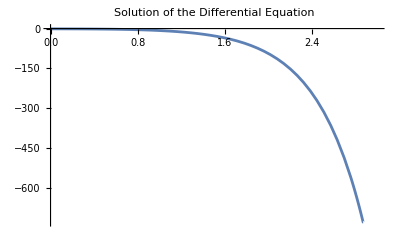

```mathematica
(*Step 1:Solve the Differential Equation*)solution=NDSolve[{y'[x]+y[x]==x,y[0]==1},y,{x,0,10}];

(*Step 2:Extract the Solution and Evaluate at Specific Points*)
ySol=y/. solution; (*Extract the solution as an interpolating function*)

(*Evaluate at specific points*)
ySol[[1]][5] (*Evaluate y[x] at x=5*)

(*Step 3:Plot the Solution*)
Plot[Log[100*YEQ[Exp[Log[10]*u], 100]],{u,0,3},PlotLabel->"Solution of the Differential Equation"]
```

```mathematica
t = 5;
Evaluate[100*YEQ[Exp[t], 100]/YEQ[1, 100]]
Evaluate[sCov[Exp[t], 100]/sCov[1, 100]]
Evaluate[nEQ[Exp[t], 100]/nEQ[1, 100]]
```

7.20213×10^-60

2.10393×10^-7

1.51528×10^-68